GammaDistribution[6.25,1.04]

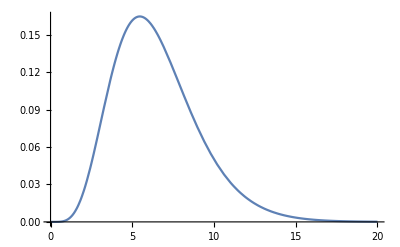

```mathematica
alpha1 = (1/0.4)^2;
dist = GammaDistribution[alpha1,6.5/alpha1]
Plot[PDF[dist, x], {x, 0, 20}]
```

```mathematica
lst = {};
For[i=0,i<=200,i++,AppendTo[lst,PDF[ dist, i]]]
For[i=1,i<=201,i++,lst[[i]] = Round[lst[[i]], 0.000001]]
```

```mathematica
Export["/Users/Jake/Desktop/Current Classes/CS 156b/firewall-covid/Imperial College Model/SIDistribution.csv",lst,"csv"];
```